```mathematica
f[x_]= (x^3-5x^2+3x+1)/(2x^2+x-1)
f[x]
```

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
g[x_] = x
```

x

```mathematica
h[x_]= Sin[x/3]-Cos[(x^3)/5]
```

-Cos[x^3/5]+Sin[x/3]

```mathematica
h[x]
```

-Cos[x^3/5]+Sin[x/3]

```mathematica
f[x]
```

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
Plot[f[x],g[x],{-10,10,x}]
```

Plot::nonopt: Options expected (instead of {-10,10,x}) beyond position 2 in Plot[f[x],g[x],{-10,10,x}]. An option must be a rule or a list of rules.

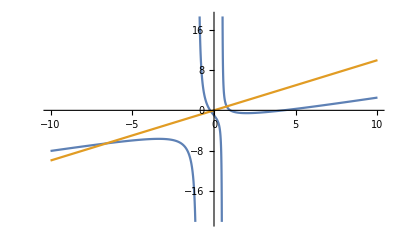

```mathematica
Plot[{f[x],g[x]},{x,-10,10}]
```

```mathematica
NSolve[f[x]==g[x],x]
```

{{x→-6.58443},{x→0.77931},{x→-0.194882}}

```mathematica
f[-6.58]
```

-6.58263

```mathematica
h'[x]
```

1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]

```mathematica
1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]
```

1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]

1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]

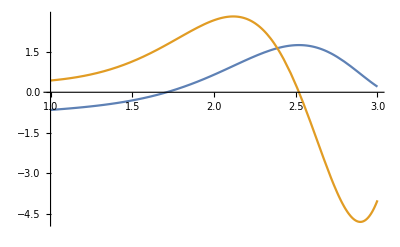

```mathematica
Plot[{h[x],h'[x]},{x,1,3}]
```

```mathematica
j[x_]=E^-x
```

```mathematica
ⅇ^-x
```

ⅇ^-x

```mathematica
j[x]
```

ⅇ^-x

```mathematica
k[x_]= Log[x]
```

Log[x]

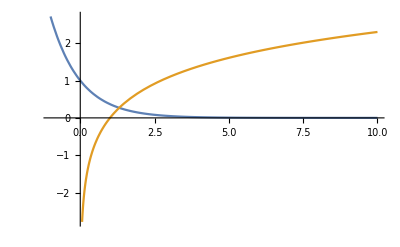

```mathematica
Plot [{j[x],k[x]},{x,-1,10}]
```

```mathematica
NSolve[j[x]==k[x],x,Reals]
```

{{x→1.3098}}

```mathematica
j[1.3097995858041505]
```

```mathematica
0.26987413757344925
```

0.269874

```mathematica
Sqrt[(1.3097995858041505^2)+ (0.26987413757344925^2)]
```

1.33731

```mathematica
f[x]
```

(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
Solve[-1+x+2 x^2==0,x]
```

{{x→-1},{x→1/2}}

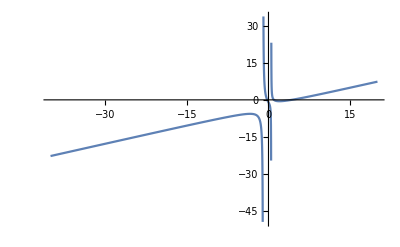

```mathematica
Plot [f[x],{x,-40,20}]
```

```mathematica
Limit [f[x],x->Infinity]
```

∞

```mathematica
Limit[f[x]/x,x->Infinity]
```

1/2

```mathematica
Limit[f[x]-(x/2),x->Infinity]
```

-11/4

```mathematica
f[x]-f[-x]
```

-(1-3 x-5 x^2-x^3)/(-1-x+2 x^2)+(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
Simplify[-(1-3 x-5 x^2-x^3)/(-1-x+2 x^2)+(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)]
```

(4 x (-2+5 x^2+x^4))/(1-5 x^2+4 x^4)

```mathematica
f[x]+f[-x]
```

(1-3 x-5 x^2-x^3)/(-1-x+2 x^2)+(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)

```mathematica
Simplify[(1-3 x-5 x^2-x^3)/(-1-x+2 x^2)+(1+3 x-5 x^2+x^3)/(-1+x+2 x^2)]
```

(-2+8 x^2-22 x^4)/(1-5 x^2+4 x^4)

```mathematica
g[x]+g[-x]
```

0

```mathematica
h[x]+h[-x]
```

-2 Cos[x^3/5]

```mathematica
h[x]-h[-x]
```

2 Sin[x/3]